```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])- t22(hop[a[3],a[6]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->1,cj->U/5,U->4,t23->x t22,t22->0.3}
```

{Δ→1,𝒿→U/5,U→4,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

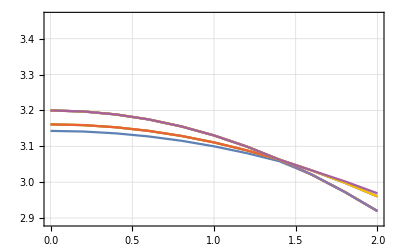

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

2.0006×10^-6

1

0.000117617

1

0.00046458

1

0.00104323

1

0.00185412

1

0.00289798

1

0.00417572

1

0.00568835

1

0.00743695

1

0.00942261

1

0.0116463

1

0.0141091

1

0.0168114

1

0.0197538

1

0.0229362

1

5.85064

1

5.82879

1

5.80545

1

5.78068

1

5.75456

1

5.72717

2

2.

2

1.99988

2

1.99953

2

1.99894

2

1.99811

2

1.99705

2

1.99575

2

1.99422

2

1.99245

2

1.99044

2

1.9882

2

1.98571

2

1.98299

2

1.98004

2

1.97685

2

5.85064

2

5.82879

2

5.80545

2

5.78068

2

5.75456

2

5.72717

3

2.

3

1.99988

3

1.99953

3

1.99894

3

1.99811

3

1.99705

3

1.99575

3

1.99422

3

1.99245

3

1.99044

3

1.9882

3

1.98571

3

1.98299

3

1.98004

3

1.97685

3

5.85064

3

5.82879

3

5.80545

3

5.78068

3

5.75456

3

5.72717

4

2.

4

1.99988

4

1.99953

4

1.99894

4

1.99811

4

1.99705

4

1.99575

4

1.99422

4

1.99245

4

1.99044

4

1.9882

4

1.98571

4

1.98299

4

1.98004

4

1.97685

4

5.85064

4

5.82879

4

5.80545

4

5.78068

4

5.75456

4

5.72717

5

6.

5

5.9994

5

5.9976

5

5.99457

5

5.99031

5

5.98477

5

5.97792

5

5.96972

5

5.96011

5

5.94907

5

5.93653

5

5.92248

5

5.90687

5

5.8897

5

5.87095

5

5.85064

5

5.82879

5

5.80545

5

5.78068

5

5.75456

5

5.72717

6

6.

6

5.9994

6

5.9976

6

5.99457

6

5.99031

6

5.98477

6

5.97792

6

5.96972

6

5.96011

6

5.94907

6

5.93653

6

5.92248

6

5.90687

6

5.8897

6

5.87095

6

0.026358

6

0.0300181

6

1.96589

6

1.96178

6

1.95745

6

1.95289

7

6.

7

5.9994

7

5.9976

7

5.99457

7

5.99031

7

5.98477

7

5.97792

7

5.96972

7

5.96011

7

5.94907

7

5.93653

7

5.92248

7

5.90687

7

5.8897

7

5.87095

7

1.97343

7

1.96977

7

1.96589

7

1.96178

7

1.95745

7

1.95289

8

6.

8

5.9994

8

5.9976

8

5.99457

8

5.99031

8

5.98477

8

5.97792

8

5.96972

8

5.96011

8

5.94907

8

5.93653

8

5.92248

8

5.90687

8

5.8897

8

5.87095

8

1.97343

8

1.96977

8

1.96589

8

1.96178

8

1.95745

8

1.95289

9

6.

9

5.9994

9

5.9976

9

5.99457

9

5.99031

9

5.98477

9

5.97792

9

5.96972

9

5.96011

9

5.94907

9

5.93653

9

5.92248

9

5.90687

9

5.8897

9

5.87095

9

1.97343

9

1.96977

9

0.0339145

9

0.0380447

9

0.0424049

9

0.0469904

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

3.75

10

0.737022

10

0.735199

10

0.73331

10

0.731365

10

0.729375

10

0.727352

10

0.725305

10

0.723245

```mathematica
data1//MatrixForm
```

(1 | 0. | 2.0006×10^-6 | 3.14297
1 | 0.1 | 0.000117617 | 3.14254
1 | 0.2 | 0.00046458 | 3.14126
1 | 0.3 | 0.00104323 | 3.13912
1 | 0.4 | 0.00185412 | 3.13612
1 | 0.5 | 0.00289798 | 3.13226
1 | 0.6 | 0.00417572 | 3.12755
1 | 0.7 | 0.00568835 | 3.12197
1 | 0.8 | 0.00743695 | 3.11552
1 | 0.9 | 0.00942261 | 3.10819
1 | 1. | 0.0116463 | 3.1
1 | 1.1 | 0.0141091 | 3.09092
1 | 1.2 | 0.0168114 | 3.08096
1 | 1.3 | 0.0197538 | 3.07011
1 | 1.4 | 0.0229362 | 3.05836
1 | 1.5 | 5.85064 | 3.04241
1 | 1.6 | 5.82879 | 3.02056
1 | 1.7 | 5.80545 | 2.99731
1 | 1.8 | 5.78068 | 2.97267
1 | 1.9 | 5.75456 | 2.94666
1 | 2. | 5.72717 | 2.9193
2 | 0. | 2. | 3.16115
2 | 0.1 | 1.99988 | 3.16065
2 | 0.2 | 1.99953 | 3.15914
2 | 0.3 | 1.99894 | 3.15663
2 | 0.4 | 1.99811 | 3.1531
2 | 0.5 | 1.99705 | 3.14858
2 | 0.6 | 1.99575 | 3.14304
2 | 0.7 | 1.99422 | 3.1365
2 | 0.8 | 1.99245 | 3.12895
2 | 0.9 | 1.99044 | 3.1204
2 | 1. | 1.9882 | 3.11084
2 | 1.1 | 1.98571 | 3.10027
2 | 1.2 | 1.98299 | 3.0887
2 | 1.3 | 1.98004 | 3.07613
2 | 1.4 | 1.97685 | 3.06255
2 | 1.5 | 5.85064 | 3.04241
2 | 1.6 | 5.82879 | 3.02056
2 | 1.7 | 5.80545 | 2.99731
2 | 1.8 | 5.78068 | 2.97267
2 | 1.9 | 5.75456 | 2.94666
2 | 2. | 5.72717 | 2.9193
3 | 0. | 2. | 3.16115
3 | 0.1 | 1.99988 | 3.16065
3 | 0.2 | 1.99953 | 3.15914
3 | 0.3 | 1.99894 | 3.15663
3 | 0.4 | 1.99811 | 3.1531
3 | 0.5 | 1.99705 | 3.14858
3 | 0.6 | 1.99575 | 3.14304
3 | 0.7 | 1.99422 | 3.1365
3 | 0.8 | 1.99245 | 3.12895
3 | 0.9 | 1.99044 | 3.1204
3 | 1. | 1.9882 | 3.11084
3 | 1.1 | 1.98571 | 3.10027
3 | 1.2 | 1.98299 | 3.0887
3 | 1.3 | 1.98004 | 3.07613
3 | 1.4 | 1.97685 | 3.06255
3 | 1.5 | 5.85064 | 3.04241
3 | 1.6 | 5.82879 | 3.02056
3 | 1.7 | 5.80545 | 2.99731
3 | 1.8 | 5.78068 | 2.97267
3 | 1.9 | 5.75456 | 2.94666
3 | 2. | 5.72717 | 2.9193
4 | 0. | 2. | 3.16115
4 | 0.1 | 1.99988 | 3.16065
4 | 0.2 | 1.99953 | 3.15914
4 | 0.3 | 1.99894 | 3.15663
4 | 0.4 | 1.99811 | 3.1531
4 | 0.5 | 1.99705 | 3.14858
4 | 0.6 | 1.99575 | 3.14304
4 | 0.7 | 1.99422 | 3.1365
4 | 0.8 | 1.99245 | 3.12895
4 | 0.9 | 1.99044 | 3.1204
4 | 1. | 1.9882 | 3.11084
4 | 1.1 | 1.98571 | 3.10027
4 | 1.2 | 1.98299 | 3.0887
4 | 1.3 | 1.98004 | 3.07613
4 | 1.4 | 1.97685 | 3.06255
4 | 1.5 | 5.85064 | 3.04241
4 | 1.6 | 5.82879 | 3.02056
4 | 1.7 | 5.80545 | 2.99731
4 | 1.8 | 5.78068 | 2.97267
4 | 1.9 | 5.75456 | 2.94666
4 | 2. | 5.72717 | 2.9193
5 | 0. | 6. | 3.2
5 | 0.1 | 5.9994 | 3.19931
5 | 0.2 | 5.9976 | 3.19723
5 | 0.3 | 5.99457 | 3.19376
5 | 0.4 | 5.99031 | 3.18891
5 | 0.5 | 5.98477 | 3.18266
5 | 0.6 | 5.97792 | 3.17501
5 | 0.7 | 5.96972 | 3.16595
5 | 0.8 | 5.96011 | 3.15549
5 | 0.9 | 5.94907 | 3.14361
5 | 1. | 5.93653 | 3.13031
5 | 1.1 | 5.92248 | 3.11558
5 | 1.2 | 5.90687 | 3.09942
5 | 1.3 | 5.8897 | 3.08184
5 | 1.4 | 5.87095 | 3.06284
5 | 1.5 | 5.85064 | 3.04241
5 | 1.6 | 5.82879 | 3.02056
5 | 1.7 | 5.80545 | 2.99731
5 | 1.8 | 5.78068 | 2.97267
5 | 1.9 | 5.75456 | 2.94666
5 | 2. | 5.72717 | 2.9193
6 | 0. | 6. | 3.2
6 | 0.1 | 5.9994 | 3.19931
6 | 0.2 | 5.9976 | 3.19723
6 | 0.3 | 5.99457 | 3.19376
6 | 0.4 | 5.99031 | 3.18891
6 | 0.5 | 5.98477 | 3.18266
6 | 0.6 | 5.97792 | 3.17501
6 | 0.7 | 5.96972 | 3.16595
6 | 0.8 | 5.96011 | 3.15549
6 | 0.9 | 5.94907 | 3.14361
6 | 1. | 5.93653 | 3.13031
6 | 1.1 | 5.92248 | 3.11558
6 | 1.2 | 5.90687 | 3.09942
6 | 1.3 | 5.8897 | 3.08184
6 | 1.4 | 5.87095 | 3.06284
6 | 1.5 | 0.026358 | 3.04572
6 | 1.6 | 0.0300181 | 3.03217
6 | 1.7 | 1.96589 | 3.01583
6 | 1.8 | 1.96178 | 2.99827
6 | 1.9 | 1.95745 | 2.97973
6 | 2. | 1.95289 | 2.9602
7 | 0. | 6. | 3.2
7 | 0.1 | 5.9994 | 3.19931
7 | 0.2 | 5.9976 | 3.19723
7 | 0.3 | 5.99457 | 3.19376
7 | 0.4 | 5.99031 | 3.18891
7 | 0.5 | 5.98477 | 3.18266
7 | 0.6 | 5.97792 | 3.17501
7 | 0.7 | 5.96972 | 3.16595
7 | 0.8 | 5.96011 | 3.15549
7 | 0.9 | 5.94907 | 3.14361
7 | 1. | 5.93653 | 3.13031
7 | 1.1 | 5.92248 | 3.11558
7 | 1.2 | 5.90687 | 3.09942
7 | 1.3 | 5.8897 | 3.08184
7 | 1.4 | 5.87095 | 3.06284
7 | 1.5 | 1.97343 | 3.04797
7 | 1.6 | 1.96977 | 3.0324
7 | 1.7 | 1.96589 | 3.01583
7 | 1.8 | 1.96178 | 2.99827
7 | 1.9 | 1.95745 | 2.97973
7 | 2. | 1.95289 | 2.9602
8 | 0. | 6. | 3.2
8 | 0.1 | 5.9994 | 3.19931
8 | 0.2 | 5.9976 | 3.19723
8 | 0.3 | 5.99457 | 3.19376
8 | 0.4 | 5.99031 | 3.18891
8 | 0.5 | 5.98477 | 3.18266
8 | 0.6 | 5.97792 | 3.17501
8 | 0.7 | 5.96972 | 3.16595
8 | 0.8 | 5.96011 | 3.15549
8 | 0.9 | 5.94907 | 3.14361
8 | 1. | 5.93653 | 3.13031
8 | 1.1 | 5.92248 | 3.11558
8 | 1.2 | 5.90687 | 3.09942
8 | 1.3 | 5.8897 | 3.08184
8 | 1.4 | 5.87095 | 3.06284
8 | 1.5 | 1.97343 | 3.04797
8 | 1.6 | 1.96977 | 3.0324
8 | 1.7 | 1.96589 | 3.01583
8 | 1.8 | 1.96178 | 2.99827
8 | 1.9 | 1.95745 | 2.97973
8 | 2. | 1.95289 | 2.9602
9 | 0. | 6. | 3.2
9 | 0.1 | 5.9994 | 3.19931
9 | 0.2 | 5.9976 | 3.19723
9 | 0.3 | 5.99457 | 3.19376
9 | 0.4 | 5.99031 | 3.18891
9 | 0.5 | 5.98477 | 3.18266
9 | 0.6 | 5.97792 | 3.17501
9 | 0.7 | 5.96972 | 3.16595
9 | 0.8 | 5.96011 | 3.15549
9 | 0.9 | 5.94907 | 3.14361
9 | 1. | 5.93653 | 3.13031
9 | 1.1 | 5.92248 | 3.11558
9 | 1.2 | 5.90687 | 3.09942
9 | 1.3 | 5.8897 | 3.08184
9 | 1.4 | 5.87095 | 3.06284
9 | 1.5 | 1.97343 | 3.04797
9 | 1.6 | 1.96977 | 3.0324
9 | 1.7 | 0.0339145 | 3.01772
9 | 1.8 | 0.0380447 | 3.00235
9 | 1.9 | 0.0424049 | 2.98607
9 | 2. | 0.0469904 | 2.96887
10 | 0. | 3.75 | 4.
10 | 0.1 | 3.75 | 4.
10 | 0.2 | 3.75 | 4.
10 | 0.3 | 3.75 | 4.
10 | 0.4 | 3.75 | 4.
10 | 0.5 | 3.75 | 4.
10 | 0.6 | 3.75 | 4.
10 | 0.7 | 3.75 | 4.
10 | 0.8 | 3.75 | 4.
10 | 0.9 | 3.75 | 4.
10 | 1. | 3.75 | 4.
10 | 1.1 | 3.75 | 4.
10 | 1.2 | 3.75 | 4.
10 | 1.3 | 0.737022 | 3.98335
10 | 1.4 | 0.735199 | 3.96183
10 | 1.5 | 0.73331 | 3.93881
10 | 1.6 | 0.731365 | 3.9143
10 | 1.7 | 0.729375 | 3.88833
10 | 1.8 | 0.727352 | 3.86091
10 | 1.9 | 0.725305 | 3.83207
10 | 2. | 0.723245 | 3.80182)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;15,1;;4]];
tmp02 = data1[[121;;122,1;;4]];
tmp03 = data1[[186;;189,1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e0data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[22;;36,1;;4]];
tmp02 = data1[[142;;147, 1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 3.14297 | 2.0006×10^-6
0.1 | 3.14254 | 0.000117617
0.2 | 3.14126 | 0.00046458
0.3 | 3.13912 | 0.00104323
0.4 | 3.13612 | 0.00185412
0.5 | 3.13226 | 0.00289798
0.6 | 3.12755 | 0.00417572
0.7 | 3.12197 | 0.00568835
0.8 | 3.11552 | 0.00743695
0.9 | 3.10819 | 0.00942261
1. | 3.1 | 0.0116463
1.1 | 3.09092 | 0.0141091
1.2 | 3.08096 | 0.0168114
1.3 | 3.07011 | 0.0197538
1.4 | 3.05836 | 0.0229362
1.5 | 3.04572 | 0.026358
1.6 | 3.03217 | 0.0300181
1.7 | 3.01772 | 0.0339145
1.8 | 3.00235 | 0.0380447
1.9 | 2.98607 | 0.0424049
2. | 2.96887 | 0.0469904)

(0. | 3.16115 | 2.
0.1 | 3.16065 | 1.99988
0.2 | 3.15914 | 1.99953
0.3 | 3.15663 | 1.99894
0.4 | 3.1531 | 1.99811
0.5 | 3.14858 | 1.99705
0.6 | 3.14304 | 1.99575
0.7 | 3.1365 | 1.99422
0.8 | 3.12895 | 1.99245
0.9 | 3.1204 | 1.99044
1. | 3.11084 | 1.9882
1.1 | 3.10027 | 1.98571
1.2 | 3.0887 | 1.98299
1.3 | 3.07613 | 1.98004
1.4 | 3.06255 | 1.97685
1.5 | 3.04797 | 1.97343
1.6 | 3.0324 | 1.96977
1.7 | 3.01583 | 1.96589
1.8 | 2.99827 | 1.96178
1.9 | 2.97973 | 1.95745
2. | 2.9602 | 1.95289)

(0. | 3.2 | 6.
0.1 | 3.19931 | 5.9994
0.2 | 3.19723 | 5.9976
0.3 | 3.19376 | 5.99457
0.4 | 3.18891 | 5.99031
0.5 | 3.18266 | 5.98477
0.6 | 3.17501 | 5.97792
0.7 | 3.16595 | 5.96972
0.8 | 3.15549 | 5.96011
0.9 | 3.14361 | 5.94907
1. | 3.13031 | 5.93653
1.1 | 3.11558 | 5.92248
1.2 | 3.09942 | 5.90687
1.3 | 3.08184 | 5.8897
1.4 | 3.06284 | 5.87095
1.5 | 3.04241 | 5.85064
1.6 | 3.02056 | 5.82879
1.7 | 2.99731 | 5.80545
1.8 | 2.97267 | 5.78068
1.9 | 2.94666 | 5.75456
2. | 2.9193 | 5.72717)

```mathematica
|
```

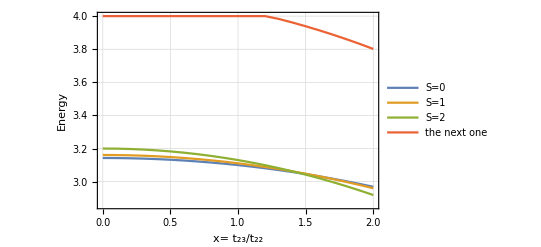

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

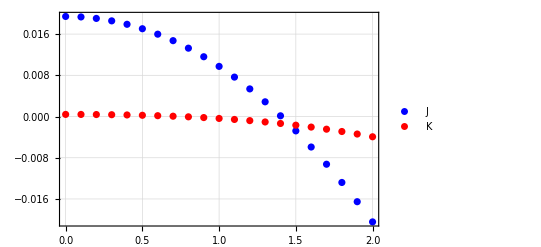

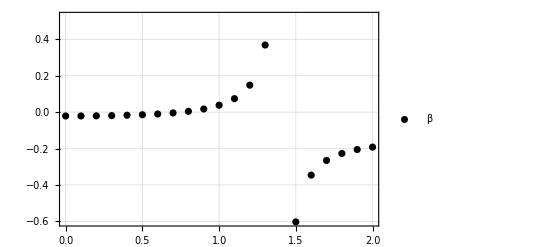

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```